```mathematica
nMax=1000;
fib[x_,p_,q_,m_]:=RecurrenceTable[{X[n]==Mod[X[n-p]+X[n-q],m],Table[X[i]==x[[i]],{i,1,q}]},X,{n,1,nMax}];
(**fib[77,7,24,8282]**)
```

Part::partd: Part specification 77⟦1⟧ is longer than depth of object.

Part::partd: Part specification 77⟦2⟧ is longer than depth of object.

Part::partd: Part specification 77⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
nMax=4000;
modulo = 2^10;
seq = Table[RandomInteger[modulo],{i,1,57}];
fib[x_,p_,q_,m_]:=RecurrenceTable[{X[n]==Mod[X[n-p]+X[n-q],m],Table[X[i]==x[[i]],{i,1,q}]},X,{n,1,nMax}];
```

```mathematica
x0 = Table[i,{i,1,55}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55}

```mathematica
fib[x0,24, 55, 1000]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,58,61,64,67,70,73,76,79,82,85,88,91,94,97,100,103,106,109,112,115,118,121,124,127,107,111,115,119,123,127,131,112,117,122,127,132,137,142,147,152,157,162,167,172,177,182,187,192,174,180,186,192,198,204,210,170,178,186,194,202,210,218,226,234,242,250,258,266,274,282,290,298,283,292,301,310,319,328,337,277,289,301,313,325,337,349,338,351,364,377,390,403,416,429,442,455,445,459,473,487,501,515,529,451,469,487,505,523,541,559,508,529,550,571,592,613,634,655,676,697,695,717,739,761,783,805,827,734,761,788,815,842,869,896,785,818,851,884,917,950,983,993,27,61,72,107,142,177,212,247,282,179,220,261,302,343,384,425,236,287,338,389,440,491,542,501,556,611,643,699,755,811,867,923,979,874,937,0,63,126,189,252,970,48,126,204,282,360,438,286,374,462,527,616,705,794,860,950,40,946,44,142,240,338,436,534,149,268,387,506,625,744,863,522,661,800,916,56,196,336,361,506,651,589,743,897,51,205,359,513,23,205,387,569,751,933,115,492,709,926,120,338,556,774,647,880,113,116,359,602,845,65,309,553,969,249,529,809,89,369,649,641,977,313,626,963,300,637,169,541,913,32,415,798,181,426,815,204,558,992,426,860,294,728,162,664,182,700,195,714,233,752,661,250,839,152,753,354,955,73,695,317,674,351,28,705,359,37,715,633,431,229,4,803,602,401,302,227,152,778,716,654,592,242,236,230,706,766,826,886,785,852,919,191,423,655,864,97,330,563,966,409,852,973,430,887,344,903,486,69,858,519,180,841,858,547,236,865,774,683,569,456,367,278,599,840,81,977,233,489,745,205,713,221,636,235,834,433,100,783,466,571,540,509,455,241,219,197,790,263,736,841,330,819,308,171,122,73,609,665,721,777,3,269,535,429,59,689,296,99,766,433,655,37,419,410,786,186,586,770,962,154,586,898,210,522,208,982,756,65,294,523,729,199,549,899,226,577,928,865,27,405,783,560,225,890,427,228,29,830,379,104,829,674,959,244,506,202,818,434,655,636,617,161,126,171,216,215,262,309,837,14,215,416,149,66,983,260,857,454,28,410,800,190,720,930,140,890,325,720,115,441,839,237,702,41,620,199,709,291,873,687,85,483,858,789,904,19,394,889,384,396,527,538,549,96,475,854,863,167,791,415,924,553,182,524,99,698,274,938,970,2,654,746,838,424,937,338,739,816,405,994,753,492,511,530,365,392,419,226,140,318,473,647,261,875,341,831,321,282,726,242,758,210,294,378,149,19,49,79,461,867,273,89,307,109,888,571,814,57,865,930,19,556,664,212,760,864,40,216,573,956,387,818,277,272,267,842,799,620,418,936,206,476,91,70,337,29,311,473,635,205,871,537,855,682,629,576,487,566,645,991,818,669,497,397,73,749,180,377,446,917,882,287,692,70,801,556,411,346,841,336,351,606,861,564,774,56,315,674,345,16,22,176,66,335,818,493,168,161,871,893,440,657,314,971,556,477,398,419,456,685,891,161,911,661,13,994,735,832,215,566,917,341,248,339,357,539,601,663,626,278,954,830,802,526,227,512,517,522,577,768,791,147,889,911,933,363,424,405,692,357,94,831,787,149,847,270,459,840,198,68,994,920,996,224,476,38,50,822,594,376,418,140,524,572,660,748,128,397,186,627,998,441,861,694,272,874,826,26,2,265,562,339,116,953,186,931,671,461,571,681,491,821,591,319,355,535,692,481,421,721,96,485,842,463,630,333,36,949,410,407,709,511,393,275,867,239,731,843,927,195,440,609,818,907,723,483,283,324,324,605,910,775,436,409,974,73,732,391,820,425,662,514,388,766,121,100,639,498,42,838,818,16,805,26,631,871,921,251,437,703,65,427,769,835,69,223,899,159,396,967,878,229,885,765,13,456,414,844,538,594,404,534,761,27,670,337,544,271,478,197,972,891,787,787,303,891,399,153,779,577,514,483,36,636,242,352,777,832,696,968,415,192,729,634,675,956,214,556,138,960,622,52,938,973,481,361,265,521,7,365,233,246,540,506,9,596,263,395,702,626,551,100,409,438,819,24,829,760,268,664,156,920,160,144,810,760,23,542,645,838,615,172,534,322,519,515,601,167,453,699,785,974,824,802,116,542,212,82,783,241,384,807,166,845,980,405,780,862,25,524,197,430,848,401,411,525,924,211,554,361,236,911,543,509,48,963,86,5,124,215,540,885,567,169,35,45,20,935,733,44,439,812,721,814,935,696,517,333,850,79,628,217,206,998,781,269,374,335,880,25,425,715,595,69,963,9,151,662,336,107,42,257,61,633,989,453,117,541,290,317,337,421,885,149,640,255,480,636,132,44,196,682,271,840,86,696,873,354,803,388,813,58,623,167,416,49,102,355,638,36,749,10,467,924,221,107,986,435,155,659,882,505,465,724,920,100,880,228,49,38,555,472,179,326,66,347,888,809,370,747,241,915,791,791,926,701,147,995,760,186,576,101,403,841,943,285,237,949,233,763,937,911,725,385,277,664,801,258,850,922,254,981,195,341,235,983,908,306,667,205,337,829,461,812,975,466,197,564,603,730,148,146,659,292,1,222,110,132,26,909,609,453,662,965,523,405,562,215,816,409,482,801,552,963,911,83,570,17,386,499,774,933,284,759,531,707,643,160,864,640,545,123,122,76,687,138,381,424,723,58,36,214,950,102,504,81,430,418,823,708,865,270,996,666,454,732,575,738,652,661,786,986,938,874,445,696,751,654,467,992,513,988,840,94,364,44,929,950,213,263,282,381,812,525,426,531,61,996,521,383,889,35,891,715,571,24,54,44,466,548,10,380,631,86,990,246,82,521,92,985,793,571,259,35,550,821,877,653,445,469,750,795,120,15,2,893,619,926,84,610,126,450,42,198,56,853,640,847,75,247,408,714,441,990,133,684,155,906,717,464,643,980,128,76,674,460,422,829,142,843,886,929,596,339,393,507,12,249,168,234,976,783,370,909,112,730,923,196,689,462,315,448,68,927,496,55,46,381,591,563,865,889,15,309,223,191,84,350,102,863,607,351,595,179,779,91,48,55,572,729,506,803,420,705,708,775,944,905,562,584,591,362,351,31,841,327,378,549,688,203,778,978,768,418,968,118,868,773,635,271,999,951,943,175,154,227,240,46,150,550,569,633,38,305,641,585,119,13,147,897,959,821,690,843,728,457,746,595,859,935,15,990,55,112,153,224,400,656,672,426,446,391,696,585,162,599,668,611,146,425,864,463,632,570,286,989,6,55,328,378,627,896,718,576,996,960,329,623,467,240,253,730,159,572,761,422,453,260,129,717,463,801,923,237,562,911,708,631,108,113,553,23,123,912,679,176,550,268,346,584,52,928,740,863,888,665,386,869,132,197,697,637,163,441,931,650,19,630,255,172,510,597,969,51,292,181,470,22,460,426,808,322,392,326,414,100,964,364,168,212,930,338,886,280,623,150,992,174,204,860,646,572,728,772,392,374,320,66,277,988,629,750,37,344,127,35,523,443,64,81,642,193,834,115,818,82,325,741,443,666,501,536,299,448,55,558,359,736,453,449,623,407,428,249,854,123,172,1,98,705,475,733,617,870,361,182,871,176,827,950,733,56,519,726,611,36,178,286,198,250,207,524,541,769,556,375,810,704,476,0,953,501,568,393,399,557,55,25,59,91,736,645,934,703,656,147,948,197,805,229,933,876,477,98,658,976,301,10,269,918,237,896,235,918,686,378,990,222,382,758,984,375,91,427,183,83,1,639,427,532,676,820,973,394,237,849,736,486,79,777,547,277,407,817,75,111,736,361,886,739,148,587,624,337,905,753,849,871,335,507,712,787,89,46,465,514,303,52,993,797,114,351,108,121,906,571,999,428,332,936,932,872,974,934,244,463,909,19,859,751,152,788,479,876,891,898,385,528,723,646,110,164,693,822,671,20,561,558,581,368,662,868,730,86,659,500,266,965,937,363,899,831,775,639,907,278,44,930,792,926,132,557,9,700,598,800,602,60,593,744,729,874,956,222,650,983,563,118,783,169,942,315,320,649,778,667,173,393,420,471,622,621,151,325,97,536,824,952,736,642,63,384,748,106,305,214,151,424,417,574,451,437,350,263,548,753,708,334,797,134,624,554,796,235,807,113,622,62,527,864,134,987,535,357,620,379,665,583,197,531,375,507,190,554,95,176,417,386,132,210,158,886,479,600,776,50,919,105,726,684,879,734,621,948,949,958,627,904,358,724,170,94,466,7,292,510,33,396,11,857,32,727,788,211,743,868,608,483,306,578,6,569,941,921,701,469,973,197,846,605,209,813,397,989,242,885,674,690,343,644,658,402,411,304,690,448,675,542,649,418,931,824,750,963,933,983,491,455,249,177,184,723,739,655,515,434,138,92,901,191,543,150,132,724,509,830,319,904,854,684,960,428,446,23,789,932,552,52,504,676,23,766,591,534,187,808,534,135,813,520,767,579,396,333,378,359,270,773,752,865,535,543,959,925,200,950,314,273,842,323,968,273,905,421,958,122,546,465,102,868,100,92,656,719,219,503,387,371,223,739,246,825,894,827,644,296,671,12,492,309,354,999,237,681,620,859,235,115,552,881,746,641,996,491,111,360,437,786,569,496,621,326,765,151,677,967,510,586,41,817,357,661,17,983,614,741,88,147,830,579,940,173,940,719,360,572,590,45,504,611,806,257,53,309,666,15,16,220,295,361,947,382,945,131,821,919,581,715,851,683,950,482,290,180,302,878,379,74,817,692,983,730,881,402,764,739,606,148,804,533,322,803,998,513,529,422,463,120,21,238,951,664,862,196,594,536,138,455,73,405,621,164,24,828,683,750,380,458,660,243,382,701,736,89,634,614,344,486,774,838,16,834,147,222,313,147,754,709,85,514,119,64,808,47,915,23,539,87,147,143,766,949,894,859,254,785,811,84,509,741,290,847,540,587,524,685,972,71,743,706,289,467,605,803,9,331,595,595,343,419,425,428,995,515,128,863,374,734,746,998,119,825,452,791,803,586,669,611,56,246,618,134,430,566,568,194,944,409,987,117,159,545,830,507,860,115,299,331,390,110,354,583,127,989,324,423,897,171,371,203,275,4,582,460,578,970,258,502,375,243,162,705,124,856,352,702,952,441,115,226,483,840,982,259,521,622,716,890,144,538,452,446,784,230,279,864,669,686,859,562,67,740,446,616,593,194,565,386,510,946,139,787,315,909,655,721,788,812,739,442,639,944,361,937,310,902,151,740,449,546,267,338,951,61,365,270,155,891,914,242,410,528,629,586,177,396,807,721,540,181,15,409,135,405,829,405,691,507,981,863,349,456,300,752,356,667,416,901,86,51,528,509,352,920,457,48,79,766,766,715,593,658,721,312,895,723,638,703,417,32,686,56,977,965,770,919,880,549,43,225,475,573,487,255,774,673,130,447,300,552,43,394,924,13,549,405,433,265,522,275,547,965,944,311,526,101,996,607,694,130,178,526,66,318,758,987,582,734,861,300,156,903,225,692,579,651,0,288,491,871,915,487,243,173,403,1,639,805,13,761,255,864,308,600,708,946,619,616,592,200,405,721,756,393,190,34,208,117,714,527,740,801,620,455,385,42,834,666,26,704,606,198,326,61,705,877,659,618,882,613,859,117,2,18,611,716,107,698,558,445,835,305,831,717,367,453,190,369,305,585,605,237,498,205,59,522,723,774,4,906,141,906,675,159,362,45,632,337,822,838,232,203,971,611,309,843,696,531,120,227,600,433,622,788,754,765,792,161,380,656,348,444,520,396,677,38,276,442,26,210,149,721,489,532,185,38,859,286,959,824,314,884,154,660,254,585,426,71,836,400,321,74,363,32,987,953,692,503,796,347,702,982,490,944,541,484,587,282,42,339,191,863,997,780,977,422,807,552,383,630,730,779,238,373,912,131,211,433,73,669,625,141,328,298,15,177,881,934,637,676,392,978,454,466,130,100,312,736,944,118,164,125,576,465,972,843,310,788,959,718,365,521,919,718,731,169,317,463,910,77,734,543,496,501,794,855,355,703,345,755,441,999,392,791,34,146,60,46,29,184,494,344,844,714,410,935,474,955,260,985,455,15,81,699,559,163,517,367,499,118,903,356,817,143,212,709,365,633,128,666,643,272,723,895,532,749,624,195,60,957,372,722,202,463,658,797,816,535,3,743,511,693,174,695,827,766,67,739,246,159,559,669,15,217,357,177,217,544,357,356,979,52,370,242,629,596,530,512,970,978,776,104,879,287,225,312,287,940,252,709,966,168,552,416,936,424,92,444,92,254,327,328,505,981,519,615,572,461,920,139,53,7,991,955,125,727,221,431,153,781,269,661,636,611,683,307,557,351,761,244,168,991,432,109,31,783,95,834,412,952,533,718,93,33,978,627,804,163,99,243,981,443,205,336,422,318,760,614,12,302,710,406,873,872,672,771,100,24,933,752,531,384,530,396,762,712,866,972,33,1,67,171,363,63,954,574,864,304,781,802,883,119,767,164,483,917,248,489,795,690,493,776,196,100,310,152,806,268,290,996,182,64,395,814,185,829,173,37,355,589,19,589,819,623,245,307,580,630,706,914,518,134,262,29,183,131,566,177,248,783,747,901,659,370,821,472,938,390,409,790,497,878,195,709,208,627,38,225,283,441,718,983,516,73,743,83,723,765,635,657,767,563,446,145,86,897,784,528,831,872,345,805,913,147,632,501,650,335,772,266,854,331,812,905,550,310,347,804,456,718,256,466,221,281,135,302,791,342,341,709,277,373,997,549,295,49,795,421,623,53,430,527,221,353,913,233,784,727,280,388,688,126,869,540,149,718,802,462,442,681,296,71,958,825,696,381,552,165,818,783,94,74,84,844,406,382,335,761,430,853,104,253,784,22,5,348,331,822,245,676,601,960,239,406,147,504,611,65,759,295,568,545,157,133,492,941,910,891,545,497,49,624,707,118,282,256,310,364,972,200,992,617,924,113,351,639,231,217,336,347,292,226,306,927,902,728,960,902,304,261,658,695,794,445,668,218,884,352,757,786,735,828,401,106,587,794,851,84,35,220,901,812,195,806,155,744,418,152,786,500,140,662,121,758,935,820,18,30,700,145,490,315,252,556,248,104,421,112,82,646,146,112,688,804,401,320,816,552,380,488,236,914,52,902,276,50,80,957,354,691,215,963,166,681,366,13,500,999,207,475,560,970,532,274,736,54,714,23,34,985,900,975,384,391,360,453,481,933,922,261,604,420,319,557,206,116,644,962,540,455,34,839,586,365,388,211,298,443,262,729,531,13,879,615,295,635,282,723,887,482,657,462,539,662,509,399,556,897,662,947,352,157,285,763,516,913,854,999,686,995,735,204,820,404,918,66,959,981,66,605,672,541,624,487,807,191,124,349,881,301,65,297,129,257,464,735,833,283,533,361,594,263,789,492,154,198,86,26,469,700,523,905,778,963,12,649,286,542,227,251,746,137,532,47,589,998,993,312,558,116,152,985,450,766,128,577,319,587,499,456,477,666,576,132,47,202,829,176,846,462,728,145,841,649,513,579,713,555,620,731,517,673,525,925,177,189,481,910,10,214,478,462,388,689,979,891,978,181,560,168,711,548,932,289,633,825,510,375,943,317,58,229,597,713,934,939,54,265,111,938,180,10,736,14,173,276,77,130,282,338,89,88,498,937,789,746,270,238,859,116,243,746,21,948,394,488,198,402,862,255,968,108,463,898,257,799,46,869,78,379,95,748,234,59,560,804,250,545,107,422,137,456,127,366,906,288,473,634,271,972,322,946,208,661,433,837,322,557,497,593,996,815,345,281,253,699,873,387,854,682,961,832,673,834,577,914,316,124,331,94,121,603,366,671,375,910,93,515,312,259,677,637,399,789,383,969,129,961,943,820,604,597,965,365,93,925,312,879,36,343,930,837,869,756,270,633,214,134,664,222,828,834,330,674,286,558,797,38,927,502,226,195,160,674,24,958,472,122,941,8,124,227,179,534,87,511,967,73,75,941,766,167,888,445,46,799,757,639,389,51,397,434,820,44,467,157,16,403,843,781,600,287,209,605,988,995,722,775,720,85,315,436,427,978,899,660,15,204,141,181,974,875,965,722,608,411,436,784,522,82,233,742,793,160,256,202,594,866,344,706,814,961,780,570,25,272,399,542,652,878,593,800,925,925,14,342,80,369,861,190,589,588,119,426,899,276,216,997,3,171,59,557,856,19,774,774,800,890,736,950,491,805,645,712,671,821,861,219,59,532,418,591,869,515,765,371,817,799,344,799,72,289,278,602,369,398,445,637,596,835,203,299,428,393,608,180,457,634,191,270,93,15,341,802,243,348,835,458,388,172,219,437,486,571,153,790,233,38,320,851,278,495,410,329,625,433,932,671,758,113,206,275,187,516,18,509,775,849,755,159,631,483,957,447,113,698,709,757,18,41,112,128,392,304,476,368,202,857,820,752,123,684,213,547,803,702,394,933,684,851,499,990,56,361,963,406,887,714,805,993,635,789,491,510,236,890,488,734,319,720,903,708,533,606,658,621,539,318,410,519,585,423,562,11,676,901,619,902,540,366,856,936,176,540,655,831,217,819,205,424,241,712,343,203,436,922,552,67,37,864,25,789,254,171,849,571,965,31,165,67,107,307,939,743,961,615,51,736,42,580,173,606,355,274,544,374,677,733,860,247,866,650,67,607,473,163,875,919,501,270,882,953,861,785,597,847,67,617,747,810,599,285,927,284,730,675,856,861,644,12,446,884,532,435,949,60,168,724,340,808,682,668,483,852,179,458,533,639,4,219,230,538,377,872,693,750,182,502,556,533,331,599,259,309,952,550,436,713,964}

```mathematica
|
```

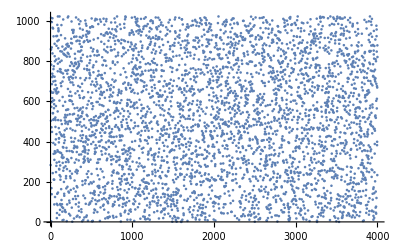
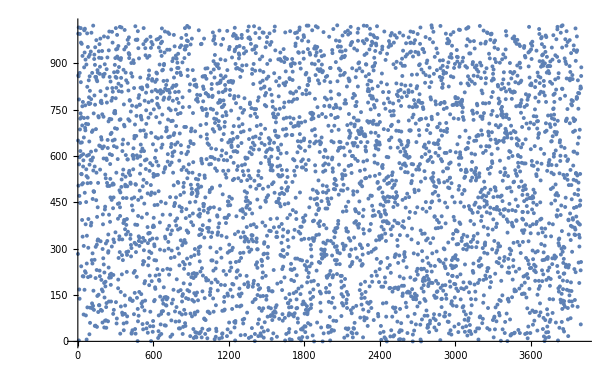
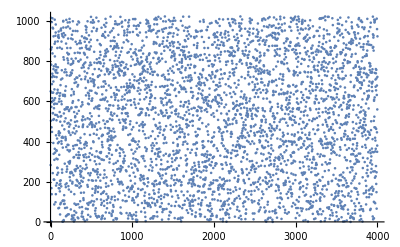
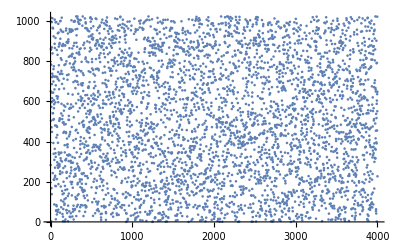
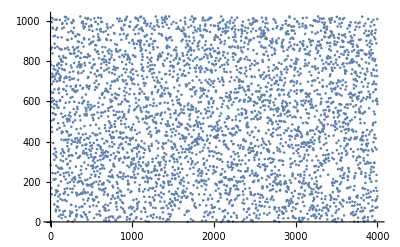
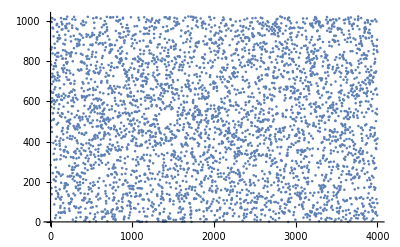
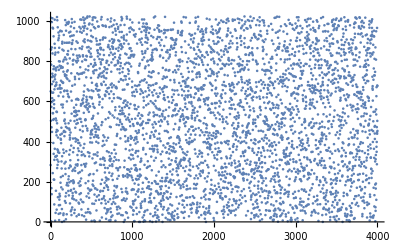
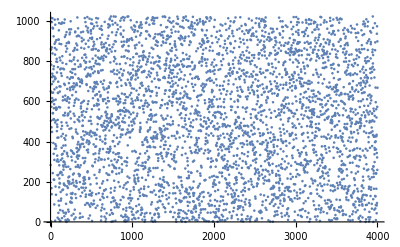
{{{-Graphics-,p=23,q=50},{-Graphics-,p=23,q=51},{-Graphics-,p=23,q=52},{-Graphics-,p=23,q=53},{-Graphics-,p=23,q=54},{-Graphics-,p=23,q=55},{-Graphics-,p=23,q=56},{-Graphics-,p=23,q=57}},{{-Graphics-,p=24,q=50},{-Graphics-,p=24,q=51},{-Graphics-,p=24,q=52},{-Graphics-,p=24,q=53},{-Graphics-,p=24,q=54},{-Graphics-,p=24,q=55},{-Graphics-,p=24,q=56},{-Graphics-,p=24,q=57}},{{-Graphics-,p=25,q=50},{-Graphics-,p=25,q=51},{-Graphics-,p=25,q=52},{-Graphics-,p=25,q=53},{-Graphics-,p=25,q=54},{-Graphics-,p=25,q=55},{-Graphics-,p=25,q=56},{-Graphics-,p=25,q=57}},{{-Graphics-,p=26,q=50},{-Graphics-,p=26,q=51},{-Graphics-,p=26,q=52},{-Graphics-,p=26,q=53},{-Graphics-,p=26,q=54},{-Graphics-,p=26,q=55},{-Graphics-,p=26,q=56},{-Graphics-,p=26,q=57}},{{-Graphics-,p=27,q=50},{-Graphics-,p=27,q=51},{-Graphics-,p=27,q=52},{-Graphics-,p=27,q=53},{-Graphics-,p=27,q=54},{-Graphics-,p=27,q=55},{-Graphics-,p=27,q=56},{-Graphics-,p=27,q=57}},{{-Graphics-,p=28,q=50},{-Graphics-,p=28,q=51},{-Graphics-,p=28,q=52},{-Graphics-,p=28,q=53},{-Graphics-,p=28,q=54},{-Graphics-,p=28,q=55},{-Graphics-,p=28,q=56},{-Graphics-,p=28,q=57}},{{-Graphics-,p=29,q=50},{-Graphics-,p=29,q=51},{-Graphics-,p=29,q=52},{-Graphics-,p=29,q=53},{-Graphics-,p=29,q=54},{-Graphics-,p=29,q=55},{-Graphics-,p=29,q=56},{-Graphics-,p=29,q=57}}}

```mathematica
Table[{ListPlot[fib[seq,p,q,modulo]],"p="~~ToString[p],"q="~~ToString[q]},{p,23,29},{q,50,57}]
```